## Chapter 3 Problem 28: Spherical Box

```mathematica
Remove["Global`*"]
```

Do (a) by finding the zeroes of the spherical Bessel functions. First plot the function, then inspect the plot for starting values for FindRoot.

First, do l=0. In this case, look at the roots relative to π

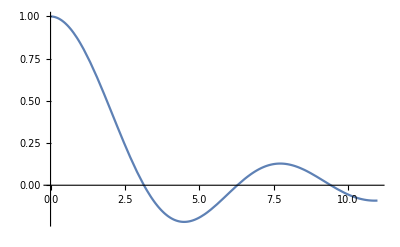

```mathematica
Plot[SphericalBesselJ[0,ρ],{ρ,0,3.5Pi}]
```

```mathematica
(ρ/.FindRoot[SphericalBesselJ[0,ρ],{ρ,{3,6,9}}])/Pi
```

{1.,2.,3.}

Next, do l=1. Compare the numbers to those in (3.7.26)

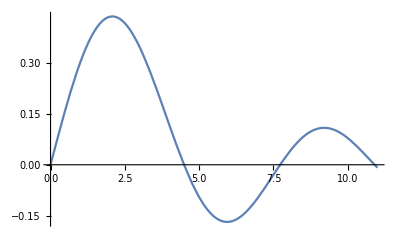

```mathematica
Plot[SphericalBesselJ[1,ρ],{ρ,0,11}]
```

```mathematica
(ρ/.FindRoot[SphericalBesselJ[1,ρ],{ρ,{4,8,11}}])
```

{4.49341,7.72525,10.9041}

Finally, do l=2. Compare the numbers to those in (3.7.27)

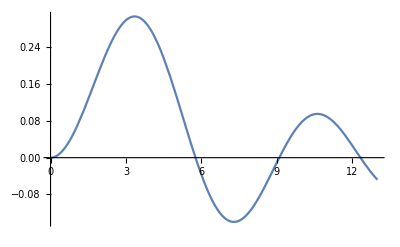

```mathematica
Plot[SphericalBesselJ[2,ρ],{ρ,0,13}]
```

```mathematica
(ρ/.FindRoot[SphericalBesselJ[2,ρ],{ρ,{6,9,12}}])
```

{5.76346,9.09501,12.3229}

Now we want to do (b), so we need to match the boundary conditions at r=a.

```mathematica
Rin=A Sin[α r/a]/(α r/a);
Rex=B Exp[-γ r/a](a/r);
eq1=(Rin/.r->a)==(Rex/.r->a)
eq2=Simplify[(D[Rin,r]/.r->a)==(D[Rex,r]/.r->a),a>0]
```

(A Sin[α])/α==B ⅇ^-γ

B+B γ+A ⅇ^γ Cos[α]==(A ⅇ^γ Sin[α])/α

Get the array of coefficients and get the determinant (with substitution for γ)

```mathematica
mat=Normal[CoefficientArrays[{eq1,eq2},{A,B}]][[2]]
```

{{Sin[α]/α,-ⅇ^-γ},{ⅇ^γ Cos[α]-(ⅇ^γ Sin[α])/α,1+γ}}

```mathematica
det=Det[mat]/.γ->Sqrt[β^2-α^2]
```

Cos[α]+(√(-α^2+β^2) Sin[α])/α

Find the zero as a function of α for the individual values of β

```mathematica
Table[FindRoot[det/.β->βVal,{α,Pi}],{βVal,{4,10,25,100}}]
```

{{α→2.47458},{α→2.85234},{α→3.02048},{α→3.11048}}

Indeed, α approaches π as β gets very large